```mathematica
ClearAll["Global`*"];
```

```mathematica
Nmax = 50;
Nexp=40;
```

```mathematica
SetPrecision[rp=1,15];
SetPrecision[κ=0,15];
SetPrecision[η=0,15];
SetPrecision[ξ=0,15];
SetPrecision[m=0,15];
SetPrecision[l=1,15];
nover =1;
scalar=0;
M1=M/.Solve[-M+rp^2/l^2==0,M][[1]];
```

```mathematica
F=Simplify[r^2/l^2-N[M1]];
H=Simplify[1/F];
V=-(((l^2 N[M1]-r^2) (14400 r^10 η^4+l^12 (r^2-6 N[M1] η)^2 (r^2-2 N[M1] η)^2 κ^2+l^10 (m^2 r^4 (r^2-6 N[M1] η)^2 (r^2-2 N[M1] η)+8 η (N[M1]^2 (-r^2+3 N[M1] η) (-r^4+6 N[M1]^2 η^2)+2 r^2 (2 r^2-7 N[M1] η) (r^2-6 N[M1] η) (r^2-2 N[M1] η) κ^2)+8 N[M1] (r^2-2 N[M1] η) (r^3-6 N[M1] r η)^2 ξ)-480 l^2 r^8 η^3 (53 N[M1] η+r^2 (-16+25 ξ))+8 l^4 r^6 η^2 (2010 N[M1]^2 η^2+r^4 (188+75 m^2 η-550 ξ)+2 r^2 η (-664 N[M1]+225 η κ^2+1450 N[M1] ξ))+2 l^8 r^2 (-168 N[M1]^4 η^4+4 N[M1] r^4 η^2 (-344 η κ^2+N[M1] (56+57 m^2 η-382 ξ))+r^8 (2+13 m^2 η-10 ξ)+16 N[M1]^2 r^2 η^3 (143 η κ^2+3 N[M1] (-7+53 ξ))+4 r^6 η (47 η κ^2+N[M1] (-8-29 m^2 η+61 ξ)))+4 l^6 r^4 η (-828 N[M1]^3 η^3+r^6 (32+55 m^2 η-130 ξ)+2 r^4 η (240 η κ^2+N[M1] (-181-115 m^2 η+800 ξ))-4 N[M1] r^2 η^2 (420 η κ^2+N[M1] (-317+1030 ξ)))))/(l^2 r^4 (10 r^2 η+l^2 (r^2-6 N[M1] η))^3 (6 r^2 η+l^2 (r^2-2 N[M1] η))));
```

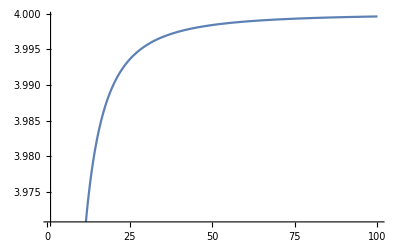

```mathematica
Plot[V,{r,rp,100}]
```

```mathematica
r=1/x;
```

```mathematica
A1=Simplify[F];
B1=Simplify[H];
V1= Simplify[V];
DDV=D[V1,x];
xp=1/rp;
```

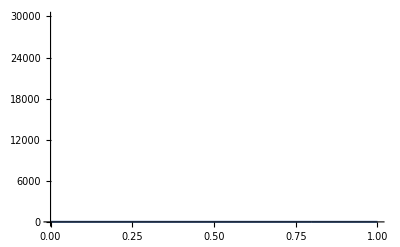

```mathematica
Plot[V1,{x,0,xp},PlotPoints-> {20000},PlotRange-> {0,30000}]
```

```mathematica
xp=1/rp;
```

```mathematica
SQRTAB=Simplify[F];
```

```mathematica
S[x_]=Chop[ SetPrecision[-1/(x-xp)Simplify[x^4 SQRTAB],15]];
T[x_]=Chop[SetPrecision[-Simplify[(2x^3 SQRTAB+x^4  D[SQRTAB,x]+2I w x^2)],15]];
U[x_]=Chop[SetPrecision[(x-xp)Simplify[(1/SQRTAB  V1 )],15]];
```

```mathematica
S1[x_]=Chop[SetPrecision[Normal[Series[S[x],{x,xp,Nmax}]],15]];
T1[x_]=Chop[SetPrecision[Normal[Series[T[x],{x,xp,Nmax}]],15]];
U1[x_]= Chop[SetPrecision[Normal[Series[U[x],{x,xp,Nmax}]],15]];
```

```mathematica
s=Chop[Simplify[(Table[1/(i!) D[S1[x],{x,i}],{i,0,Nmax}])/.x->xp]];
t=Simplify[(Table[1/(i!) D[T1[x],{x,i}],{i,0,Nmax}])/.x->xp];
u=Simplify[(Table[1/(i!) D[U1[x],{x,i}],{i,0,Nmax}])/.x->xp];
```

```mathematica
DENOMINADOR=SetPrecision[Table[Simplify[i*(i-1)*s[[1]] + i*t[[1]]],{i,1,Nmax}],15];
```

```mathematica
an={1};
Do[
aproximo = Sum[
                 (  (j-1)*(j-2)*s[[i-j+2]] + (j-1)*t[[i-j+2]] + u[[i-j+2]]  )*an[[j]]
                     ,{j,1,i}];
  an=Append[an,Together[aproximo/(-DENOMINADOR[[i]])]]
,{i,1,Nmax}]
```

```mathematica
wfund[NSoma_]:= 
Module[{zeromaquina,psi, poly, modos0,modos1,modos2},

psi[w_]=Together[Sum[an[[i]]*(-xp)^i,{i,1, NSoma}]];
poly=Numerator[psi[w]];
modos0= w/.SetPrecision[NSolve[poly==0&& -500<Im[w]<0,w],15];
zeromaquina = 10^(-5);
cond1[x_/;Re[x]<=zeromaquina]:=True;
modos1=Select[modos0,cond1];
modos2=Sort[modos1,Im[#1]>Im[#2]&];
{NSoma,modos2}
]
```

```mathematica
TabelaIm = {};
TabelaRe = {};

Do[
wcalculado =  wfund[i];
TabelaIm = Append[TabelaIm,{wcalculado[[1]],Im[wcalculado[[2]][[nover]]]} ];
TabelaRe = Append[TabelaRe,{wcalculado[[1]],Re[wcalculado[[2]][[nover]]]} ];
,{i,4,Nmax}
  ]//Timing
```

{0.515625,Null}

```mathematica
TabelaRe[[Nmax-3]][[2]] + I TabelaIm[[Nmax-3]][[2]]
```

-1.93649776028125-1.4999825407703 ⅈ

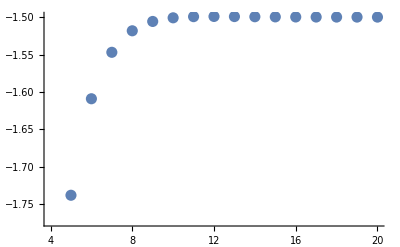

```mathematica
grafIm=ListPlot[TabelaIm,PlotStyle->PointSize[0.02]]
```

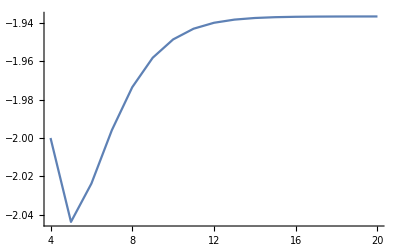

```mathematica
grafRe=ListPlot[TabelaRe,PlotStyle->PointSize[0.02],Joined->True]
```